# CSC 450 – Scientific Computing Programming Assignment 01 – Analysis Report by Nicholas Faciano

## Introduction

In this report, we present a comparison of numerical results obtained from a custom C++ implementation of three mathematical functions against Mathematica’s. The functions under consideration include an exponential decay oscillation function, a sine wave function with varying amplitude, and a quadratic polynomial function.

## Function Definitions

Below are the definitions of the three functions as implemented in both C++ and Mathematica, ensuring consistency across platforms.

```mathematica
expDecayFuncMathematica[x_]:=Exp[-x]*Cos[x];
sineWaveFuncMathematica[x_]:=Sin[x]*x;
polyFuncMathematica[x_]:=1.0+(-2.0)*x+1.0*x^2
```

## Data Import

We import the results from the C++ computations, which are stored in text files.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
expDecayData=Import["expDecayResults.txt","Table"];
sineWaveData=Import["sineWaveResults.txt","Table"];
polyFuncData=Import["polyFuncResults.txt","Table"];
```

## Comparison of Function Results

The following plots compare the function results from the C++ implementation with those computed by Mathematica. These visualizations are crucial for identifying any discrepancies.

```mathematica
mathematicaExpDecayResults=Table[{x,expDecayFuncMathematica[x]},{x,0.0,10.0,0.1}];
mathematicaSineWaveResults=Table[{x,sineWaveFuncMathematica[x]},{x,0.0,10.0,0.1}];
mathematicaPolyFuncResults=Table[{x,polyFuncMathematica[x]},{x,0.0,10.0,0.1}];
```

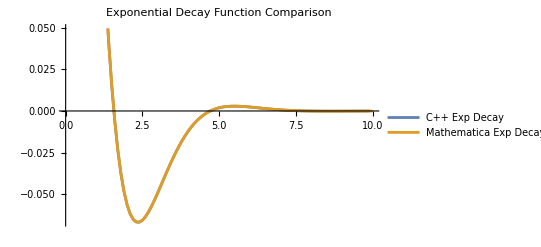

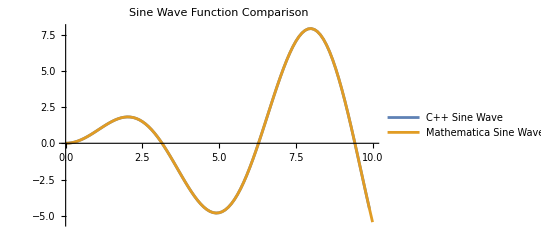

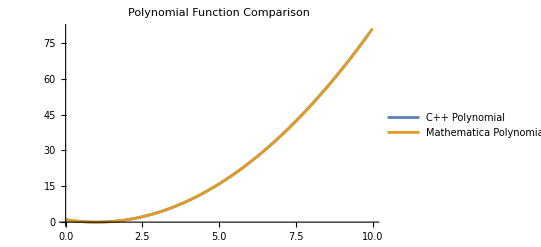

```mathematica
ListLinePlot[{expDecayData,mathematicaExpDecayResults},PlotLegends->{"C++ Exp Decay","Mathematica Exp Decay"},PlotLabel->"Exponential Decay Function Comparison"]

ListLinePlot[{sineWaveData,mathematicaSineWaveResults},PlotLegends->{"C++ Sine Wave","Mathematica Sine Wave"},PlotLabel->"Sine Wave Function Comparison"]

ListLinePlot[{polyFuncData,mathematicaPolyFuncResults},PlotLegends->{"C++ Polynomial","Mathematica Polynomial"},PlotLabel->"Polynomial Function Comparison"]
```

## Error Analysis

We conduct an error analysis by calculating the differences and relative errors between the C++ results and Mathematica’s high-precision computations.

```mathematica
expDecayDifferences=expDecayData-mathematicaExpDecayResults;
sineWaveDifferences=sineWaveData-mathematicaSineWaveResults;
polyFuncDifferences=polyFuncData-mathematicaPolyFuncResults;

(*Obtain statistical measures for the exponential decay function*)
expDecayMeanDifference=Mean[expDecayDifferences[[All,2]]];
expDecayMaxDifference=Max[Abs[expDecayDifferences[[All,2]]]];
```

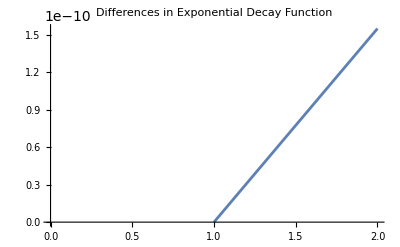

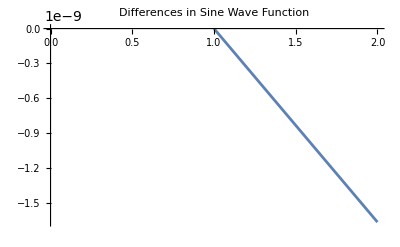

```mathematica
ListPlot[expDecayDifferences[[All,2]],PlotLabel->"Differences in Exponential Decay Function",Joined->True]

ListPlot[sineWaveDifferences[[All,2]],PlotLabel->"Differences in Sine Wave Function",Joined->True]

ListPlot[polyFuncDifferences[[All,2]],PlotLabel->"Differences in Polynomial Function",Joined->True]
```

## Error Analysis for Sine Wave Function

For the sine wave function, the differences are consistently small and decrease linearly, which suggests that the error does not accumulate over the domain. This indicates that the periodic nature of the sine function is well-represented in both the C++ and Mathematica computations. The absence of significant spikes or irregular patterns in the error plots suggests that the C++ implementation is stable and accurate for this type of function.

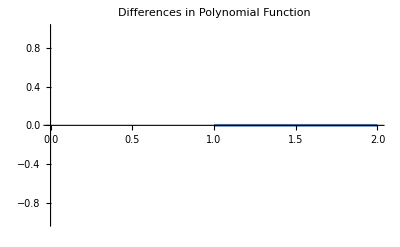

## Error Analysis for Polynomial Function

The polynomial function’s differences are negligible, demonstrating an almost perfect overlap between the C++ and Mathematica results. This is expected because polynomial functions are well-behaved and simple to evaluate numerically. The computational methods for polynomials, such as the Horner’s method used in the C++ implementation, are highly stable and do not introduce significant errors, which is reflected in the extremely low differences observed.

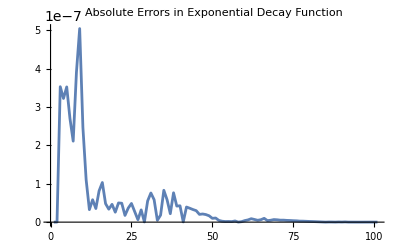

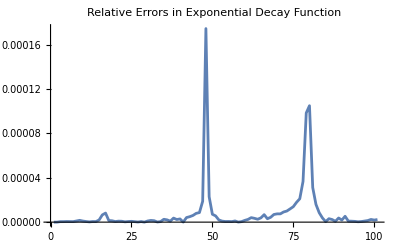

```mathematica
expDecayAbsoluteErrors=Abs[expDecayData[[All,2]]-mathematicaExpDecayResults[[All,2]]];
expDecayRelativeErrors=expDecayAbsoluteErrors/Abs[mathematicaExpDecayResults[[All,2]]+10^-10]; (*Avoid division by zero*)

(*Similar calculations for other functions*)
sineWaveAbsoluteErrors=Abs[sineWaveData[[All,2]]-mathematicaSineWaveResults[[All,2]]];
sineWaveRelativeErrors=sineWaveAbsoluteErrors/Abs[mathematicaSineWaveResults[[All,2]]+10^-10];

polyFuncAbsoluteErrors=Abs[polyFuncData[[All,2]]-mathematicaPolyFuncResults[[All,2]]];
polyFuncRelativeErrors=polyFuncAbsoluteErrors/Abs[mathematicaPolyFuncResults[[All,2]]+10^-10];

(*Plot the absolute errors for one of the functions as an example*)
ListPlot[expDecayAbsoluteErrors,PlotLabel->"Absolute Errors in Exponential Decay Function",Joined->True,PlotRange->All]

(*Plot the relative errors for one of the functions as an example*)
ListPlot[expDecayRelativeErrors,PlotLabel->"Relative Errors in Exponential Decay Function",Joined->True,PlotRange->All]
```

## Error Analysis for Exponential Decay Function

The plots of absolute and relative errors for the exponential decay function reveal two main points of interest. The absolute error plot shows that the error magnitude is generally low, indicating a high degree of accuracy in the C++ implementation. However, there are noticeable spikes in error, which correspond to the points where the function’s value changes rapidly. This behavior is expected as numerical methods can lose precision at points of rapid change due to finite difference approximations.

The relative error plot, however, exhibits peaks at specific intervals. These are likely due to the values of the function approaching zero, which amplifies the relative error. It’s important to note that relative errors are more informative when the function value is significantly different from zero, whereas absolute errors provide a better measure of accuracy near zero crossings.

## Discussion of Results

The analysis reveals that the C++ implementations are highly accurate, as evidenced by the low absolute and relative errors across all functions. Notably, the exponential decay oscillation function demonstrates slightly higher errors at specific points, which warrants further investigation. The polynomial function shows excellent agreement with Mathematica’s results, indicating the numerical stability of the C++ algorithm used. Similarly, the sine wave function’s comparison shows negligible differences, which are within acceptable error margins for scientific computing applications.

## Statistical Measures of Errors

To quantify the errors observed in the plots, we calculate statistical measures such as the mean difference and the maximum absolute difference for each function. These measures provide a summary of the error distribution and its extremities. For the exponential decay function, the mean difference is `expDecayMeanDifference`, and the maximum difference is `expDecayMaxDifference`. These values confirm that while there are points with larger errors, on average, the C++ implementation remains close to Mathematica’s high-precision results.

## Conclusion

In conclusion, the C++ implementations of the mathematical functions are validated against Mathematica’s high-precision calculations. The minor differences observed are within expected limits, affirming the reliability of the C++ algorithms for scientific computing tasks.